## Мухамадиев Владимир

# Задание 9

## Загрузка и предварительная обработка

```mathematica
(*Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
karate=ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
```

```mathematica
pc={{1,2,3,4,5,6,7,8,9,11,12,13,14,17,18,20,22},{10,15,16,19,21,23,24,25,26,27,28,29,30,31,32,33,34}};
```

## 1. Similarity matrix

```mathematica
GraphSimilarityMatrix[graph_]:=Module[{gdm=GraphDistanceMatrix[graph],jm={},am=AdjacencyMatrix[graph],dl=VertexDegree[graph],vc=VertexCount[graph]},jm=Table[If[i==j,0,Length[Position[{gdm⟦i⟧,gdm⟦j⟧}ᵀ,{1,1}]]],{i,1,vc},{j,1,vc}];Table[(jm⟦i,j⟧+am⟦i,j⟧)/(Min[dl⟦i⟧,dl⟦j⟧]+1-am⟦i,j⟧),{i,1,vc},{j,1,vc}]]
```

### Матрица схожести заданного графа

```mathematica
MatrixPlot[GraphSimilarityMatrix[karate],PlotLegends->Automatic]
```

-Graphics-

## 2. Ravasz Algorithm

```mathematica
Ravasz[graph_]:=Module[{gsm=GraphSimilarityMatrix[graph],clusters=Partition[VertexList[graph],1],ce={Partition[VertexList[graph],1]},max={},temp={}},Do[max=Sort[RandomChoice[Position[gsm,Max[gsm]]]];clusters⟦max⟦1⟧⟧=Flatten[{clusters⟦max⟦1⟧⟧,clusters⟦max⟦2⟧⟧}];clusters=Delete[clusters,max⟦2⟧];AppendTo[ce,clusters];temp=(gsm⟦max⟦1⟧⟧+gsm⟦max⟦2⟧⟧)/Length[clusters⟦max⟦1⟧⟧];temp⟦max⟦1⟧⟧=0;gsm⟦max⟦1⟧⟧=temp;gsm=gsmᵀ;gsm⟦max⟦1⟧⟧=temp;gsm=Delete[gsm,max⟦2⟧];gsm=gsmᵀ;gsm=Delete[gsm,max⟦2⟧],{i,1,VertexCount[graph]-1}];ce]
```

### Разбиение на сообщества по алгоритму

```mathematica
ac=Ravasz[karate]⟦-2⟧;
```

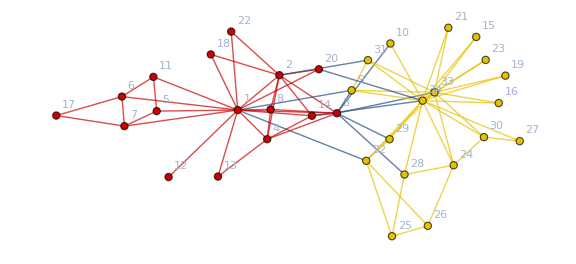

```mathematica
HighlightGraph[karate,Subgraph[karate,#]& /@ac,VertexLabels->"Name",ImageSize->Large]
```

### Эталонное разбиение на сообщества

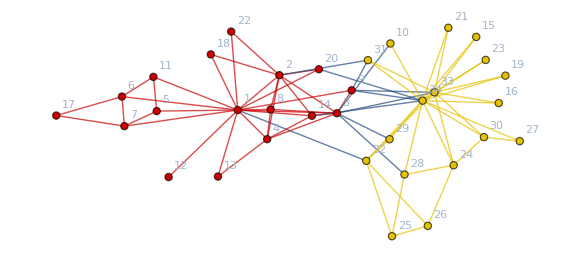

```mathematica
HighlightGraph[karate,Subgraph[karate,#]& /@ pc,VertexLabels->"Name",ImageSize->Large]
```

### Вершины, которые оказались в других сообществах по сравнению с эталоном

```mathematica
nt=Flatten[{Intersection[ac⟦1⟧,pc⟦2⟧],Intersection[ac⟦2⟧,pc⟦1⟧]}]
```

{9}

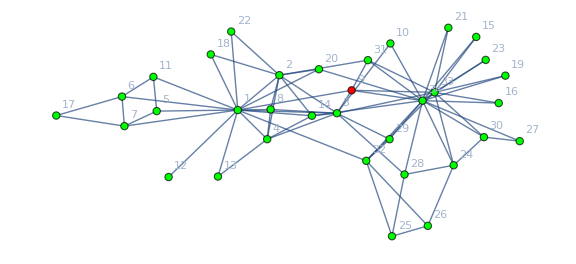

```mathematica
Graph[karate,VertexStyle->Flatten[Append[Map[#->Green&,Complement[ac⟦1⟧∪ac⟦2⟧,nt]],Map[#->Red&,nt]]],VertexLabels->"Name",ImageSize->Large]
```

## 3. Центральность ребер в сети

```mathematica
EdgeRandomWalkCentrality[graph_,n_]:=Module[{vl=VertexList[graph],el=EdgeList[graph],temp={},k=0,tempdata={},out=ConstantArray[{},n]},Do[k=0;tempdata=ConstantArray[{},VertexCount[graph]^2];Do[k++;If[i==j,tempdata⟦k⟧={},temp=IGRandomEdgeWalk[graph,vl⟦i⟧,10EdgeCount[graph]];While[FirstPosition[temp,vl⟦j⟧]===Missing["NotFound"],temp=IGRandomEdgeWalk[graph,vl⟦i⟧,10EdgeCount[graph]]];tempdata⟦k⟧=temp⟦1;;FirstPosition[temp,vl⟦j⟧]⟦1⟧⟧],{i,1,VertexCount[graph]},{j,1,VertexCount[graph]}];tempdata=DeleteCases[tempdata,{}];tempdata=Flatten[Table[Normal[Counts[tempdata⟦i⟧]],{i,1,Length[tempdata]}]];tempdata=Counts[DeleteCases[{tempdata⟦All,1⟧,tempdata⟦All,2⟧}ᵀ,{_,_?EvenQ}]⟦All,1⟧];tempdata=Table[tempdata[el⟦i⟧],{i,1,Length[el]}];out⟦l⟧=tempdata,{l,1,n}];N[Mean[out]]]
```

### Для заданного графа

```mathematica
erwc=EdgeRandomWalkCentrality[karate,100];
```

### Визуализация топ 10

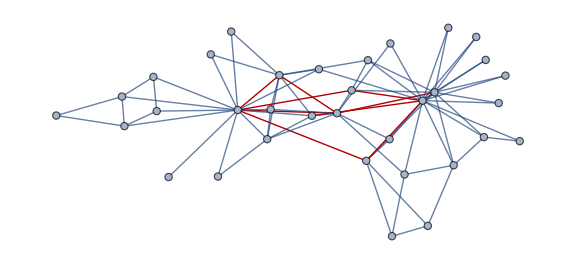

```mathematica
Graph[karate,GraphHighlight->ReverseSortBy[{EdgeList[karate],erwc}ᵀ,Last]⟦1;;10,1⟧,ImageSize->Large]
```

### Сравнение с топ 10 центральности по посредничеству

```mathematica
Grid[Prepend[Prepend[Flatten[{ReverseSortBy[{EdgeList[karate],erwc}ᵀ,Last]⟦1;;10⟧ᵀ,ReverseSortBy[{EdgeList[karate],EdgeBetweennessCentrality[karate]}ᵀ,Last]⟦1;;10⟧ᵀ},1]ᵀ,{"Ребра","Значения","Ребра","Значения"}],{"Топ 10 центральности\nпо случайному блужданию",SpanFromLeft,"Топ 10 центральности\nпо посредничеству",SpanFromLeft}],Frame->All,Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray,2->Gray}}},Spacings->{1,1}]
```

Топ 10 центральности
по случайному блужданию |  | Топ 10 центральности
по посредничеству | 
Ребра | Значения | Ребра | Значения
3<->1 | 303.92 | 32<->1 | 142.786
32<->1 | 302.69 | 7<->1 | 87.6667
33<->3 | 302.32 | 6<->1 | 87.6667
9<->1 | 298.75 | 3<->1 | 87.2778
2<->1 | 297.18 | 9<->1 | 83.2968
34<->14 | 295.97 | 33<->3 | 77.4032
34<->33 | 294.39 | 34<->14 | 76.0984
34<->9 | 293.04 | 34<->20 | 66.627
3<->2 | 292.85 | 12<->1 | 66.
34<->32 | 291.46 | 34<->27 | 60.9143